```mathematica
KeepContracting[g_]:=Block[{sols, compleEdges=EdgeList[GraphComplement[g]]},
If[Length[compleEdges]>0,
sols=Solve[ToEquations[g],SymbolRange[g]];
Monitor[
Table[
With[
{subList=Map[{Symbol["x"<>ToString[e[[1]]]],Symbol["x"<>ToString[e[[2]]]]}/.#&,sols]},
With[{
len=Length[Select[subList,#[[1]]==1&&#[[2]]==1&]]/6,
h=VertexContract[g,{e[[1]],e[[2]]}]
},
With[
{chr=ChromaticPolynomial[h,4]/24,
klik=First[ FindClique[h]]
},
{ChromaticPolynomial[g,4]/24,Graph[h,VertexLabels->"Name",GraphHighlight->klik],Length[klik],VertexCount[g],e,len,chr, KeepContracting[h]}
]
]
]
,{e,Take[compleEdges,1]}
],
e]
]
]
```

```mathematica
KeepContracting2[g_]:=Module[{sols, compleEdges=EdgeList[GraphComplement[g]]},
If[Length[compleEdges]>0,
sols=Solve[ToEquations[g],SymbolRange[g]];
Monitor[
Table[
With[
{subList=Map[{Symbol["x"<>ToString[e[[1]]]],Symbol["x"<>ToString[e[[2]]]]}/.#&,sols]},
With[{
len=Length[Select[subList,#[[1]]==1&&#[[2]]==1&]]/6,
h=VertexContract[g,{e[[1]],e[[2]]}]
},
With[
{chr=ChromaticPolynomial[h,4]/24,
klik=First[ FindClique[h]]
},
{ChromaticPolynomial[g,4]/24->chr,KeepContracting2[h]}
]
]
]
,{e,Take[compleEdges,Min[Length[compleEdges],3]]}
],
e,5],
{}
]
]
```

```mathematica
FindClique
```

```mathematica
ChromaticPolynomial[ReadGrof[60],4]
```

24

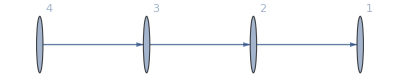

```mathematica
Graph[DeleteDuplicates[Flatten[KeepContracting2[JacobsThalGraph2[6]]]],VertexLabels->"Name"]
```

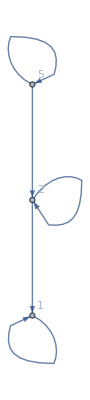

```mathematica
Graph[DeleteDuplicates[Flatten[KeepContracting2[JacobsThalGraph2[7]]]],VertexLabels->"Name"]
```

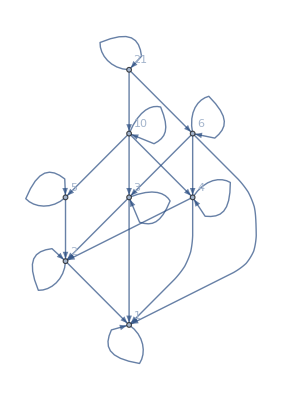

```mathematica
Graph[DeleteDuplicates[Flatten[KeepContracting2[JacobsThalGraph2[9]]]],VertexLabels->"Name"]
```

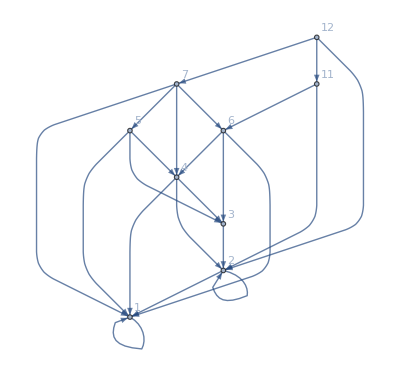

```mathematica
Graph[DeleteDuplicates[Flatten[KeepContracting2[JacobsThalGraph2[8]]]],VertexLabels->"Name"]
```

```mathematica
Graph[KeepContracting2[Graph[plantri[[1]]]],VertexLabels->"Name"]
```

Take::take: Cannot take positions 1 through 2 in {12 <-> 3}.

Table::iterb: Iterator {e, Take[{12 <-> 3}, 2]} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Take::take: Cannot take positions 1 through 2 in {12 <-> 3}.

Take::take: Cannot take positions 1 through 2 in {10 <-> 6}.

General::stop: Further output of Take :: take will be suppressed during this calculation.

Graph[$Aborted,VertexLabels→Name]

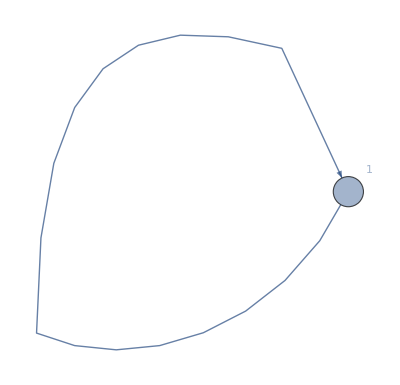
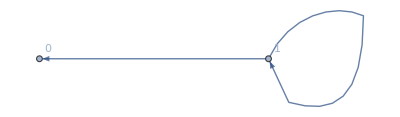
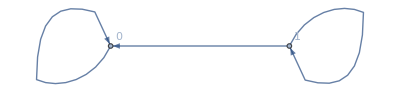
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Monitor[Table[Graph[DeleteDuplicates[Flatten[KeepContracting2[ReadGrof[k]]]],VertexLabels->"Name"],{k,1,5}],k]
```

```mathematica
Monitor[Table[Graph[DeleteDuplicates[Flatten[KeepContracting2[ReadGrof[k]]]],VertexLabels->"Name"],{k,1000,1005}],k]
```

$Aborted

```mathematica
Graph[DeleteDuplicates[Flatten[KeepContracting2[Graph[plantri[[1]]]]]],VertexLabels->"Name"]
```

Graph[{10→4,4→1,1→1,1→0,0→0,4→2,2→2,2→0,2→1,4→0,$Aborted},VertexLabels→Name]

```mathematica
Flatten[KeepContracting2[VertexDelete[Graph[plantri[[1]]],1]]]
```

{20→6,6→2,2→2,2→1,1→1,1→1,1→1}

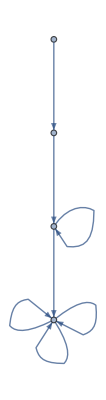

```mathematica
Graph[{20->6,6->2,2->2,2->1,1->1,1->1,1->1}]
```

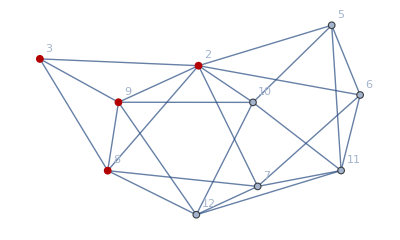
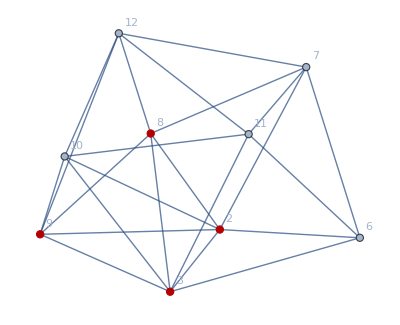
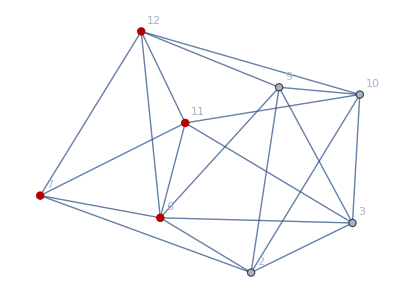
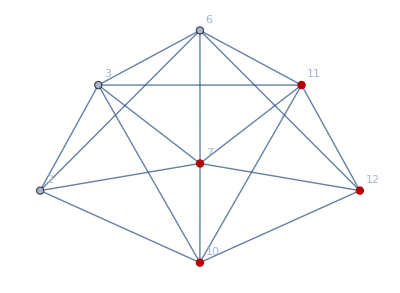
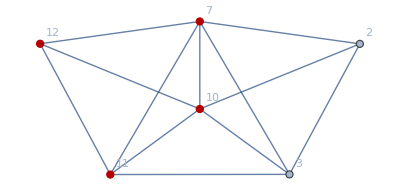
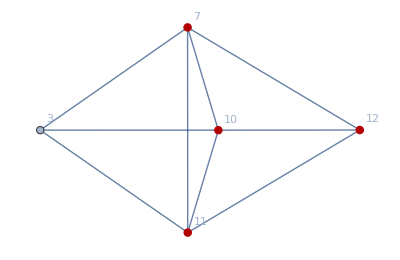
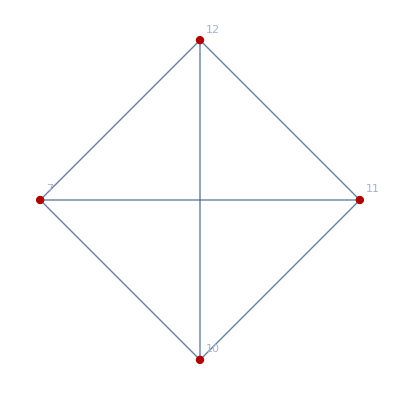
{{20,-Graphics-,4,11,2<->4,6,6,{{6,-Graphics-,4,10,3<->5,2,2,{{2,-Graphics-,4,9,6<->8,2,2,{{2,-Graphics-,4,8,7<->9,1,1,{{1,-Graphics-,4,7,10<->6,1,1,{{1,-Graphics-,4,6,11<->2,1,1,{{1,-Graphics-,4,5,12<->3,1,1,Null}}}}}}}}}}}}}}

```mathematica
KeepContracting[VertexDelete[Graph[plantri[[1]]],1]]
```

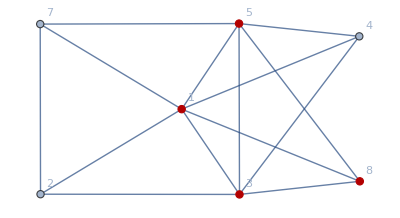
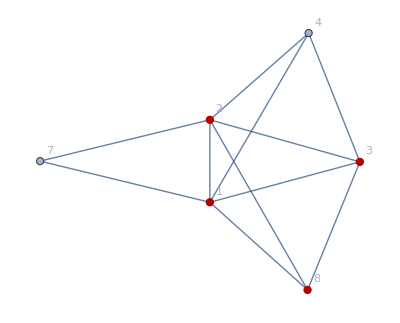
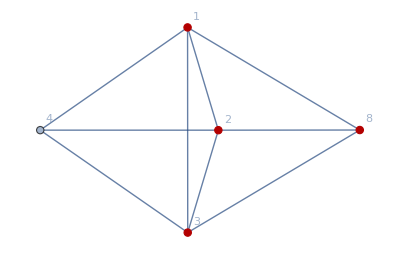
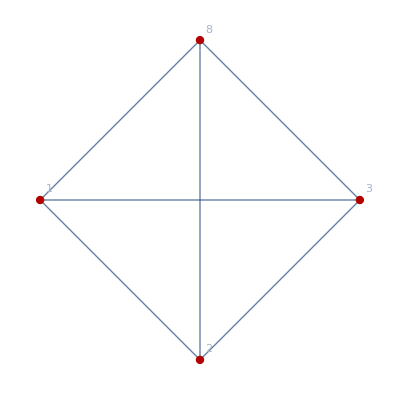
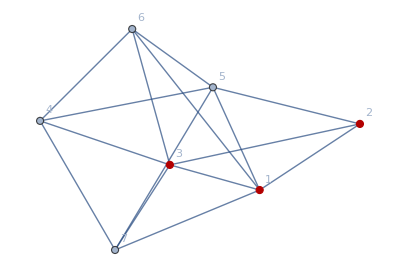
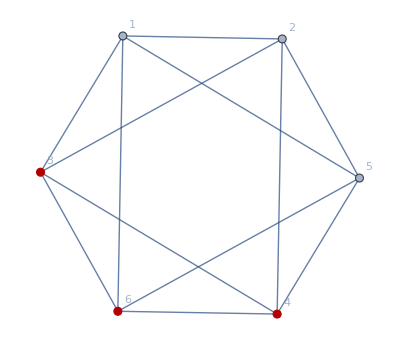
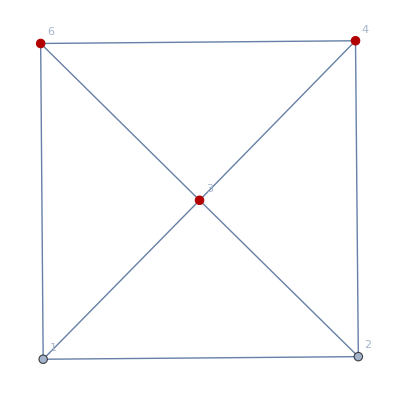
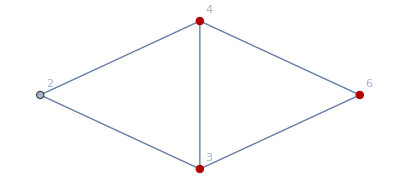
{{4,-Graphics-,4,8,1<->6,3,3,{{3,-Graphics-,4,7,2<->5,2,2,{{2,-Graphics-,4,6,3<->7,1,1,{{1,-Graphics-,4,5,8<->4,1,1,Null}}}}}}}}
{{12,-Graphics-,3,8,1<->8,7,7,{{7,-Graphics-,3,7,2<->7,4,4,{{4,-Graphics-,3,6,3<->5,3,3,{{3,-Graphics-,3,5,4<->1,2,2,{{2,-Graphics-,3,4,6<->2,1,1,Null}}}}}}}}}}
{{1,-Graphics-,4,8,1<->7,1,1,{{1,-Graphics-,4,7,2<->4,1,1,{{1,-Graphics-,4,6,6<->2,1,1,{{1,-Graphics-,4,5,8<->1,1,1,Null}}}}}}}}
{{1,-Graphics-,4,8,1<->6,1,1,{{1,-Graphics-,4,7,2<->4,1,1,{{1,-Graphics-,4,6,3<->8,1,1,{{1,-Graphics-,4,5,5<->7,1,1,Null}}}}}}}}
{{1,-Graphics-,4,9,1<->5,1,1,{{1,-Graphics-,4,8,2<->6,1,1,{{1,-Graphics-,4,7,3<->4,1,1,{{1,-Graphics-,4,6,7<->9,1,1,{{1,-Graphics-,4,5,8<->7,1,1,Null}}}}}}}}}}
{{4,-Graphics-,4,9,1<->5,4,4,{{4,-Graphics-,4,8,2<->8,3,3,{{3,-Graphics-,4,7,3<->6,2,2,{{2,-Graphics-,4,6,7<->9,1,1,{{1,-Graphics-,4,5,4<->7,1,1,Null}}}}}}}}}}
{{5,-Graphics-,4,9,1<->5,5,5,{{5,-Graphics-,4,8,2<->8,2,2,{{2,-Graphics-,4,7,3<->9,1,1,{{1,-Graphics-,5,6,7<->6,0,0,Null}}}}}}}}
{{1,-Graphics-,4,9,1<->5,1,1,{{1,-Graphics-,4,8,2<->8,1,1,{{1,-Graphics-,5,7,3<->4,0,0,{{0,-Graphics-,5,6,7<->6,0,0,Null}}}}}}}}
{{1,-Graphics-,4,9,1<->5,1,1,{{1,-Graphics-,4,8,2<->8,1,1,{{1,-Graphics-,5,7,3<->4,0,0,{{0,-Graphics-,5,6,7<->6,0,0,Null}}}}}}}}
{{1,-Graphics-,5,9,1<->5,0,0,{{0,-Graphics-,5,8,2<->8,0,0,{{0,-Graphics-,5,7,3<->4,0,0,{{0,-Graphics-,5,6,9<->6,0,0,Null}}}}}}}}
{{4,-Graphics-,4,9,1<->5,3,3,{{3,-Graphics-,4,8,2<->7,2,2,{{2,-Graphics-,4,7,3<->9,1,1,{{1,-Graphics-,4,6,8<->2,1,1,{{1,-Graphics-,4,5,4<->3,1,1,Null}}}}}}}}}}
{{5,-Graphics-,4,9,1<->5,0,0,{{0,-Graphics-,5,8,2<->8,0,0,{{0,-Graphics-,5,7,3<->4,0,0,{{0,-Graphics-,5,6,7<->6,0,0,Null}}}}}}}}
{{1,-Graphics-,4,9,1<->5,1,1,{{1,-Graphics-,4,8,2<->8,1,1,{{1,-Graphics-,4,7,3<->4,1,1,{{1,-Graphics-,4,6,7<->6,1,1,{{1,-Graphics-,4,5,9<->1,1,1,Null}}}}}}}}}}
{{1,-Graphics-,4,9,1<->5,1,1,{{1,-Graphics-,4,8,2<->8,1,1,{{1,-Graphics-,4,7,3<->9,1,1,{{1,-Graphics-,4,6,7<->6,1,1,{{1,-Graphics-,4,5,4<->3,1,1,Null}}}}}}}}}}
{{1,-Graphics-,4,9,1<->5,1,1,{{1,-Graphics-,4,8,2<->8,1,1,{{1,-Graphics-,4,7,3<->4,1,1,{{1,-Graphics-,4,6,7<->6,1,1,{{1,-Graphics-,4,5,9<->2,1,1,Null}}}}}}}}}}
{{4,-Graphics-,4,9,1<->5,4,4,{{4,-Graphics-,4,8,2<->8,3,3,{{3,-Graphics-,4,7,3<->9,2,2,{{2,-Graphics-,4,6,7<->6,1,1,{{1,-Graphics-,4,5,4<->1,1,1,Null}}}}}}}}}}
{{3,-Graphics-,4,9,1<->6,2,2,{{2,-Graphics-,4,8,2<->5,0,0,{{0,-Graphics-,5,7,3<->9,0,0,{{0,-Graphics-,5,6,7<->8,0,0,Null}}}}}}}}
{{12,-Graphics-,4,9,1<->5,1,1,{{1,-Graphics-,5,8,2<->4,0,0,{{0,-Graphics-,5,7,7<->9,0,0,{{0,-Graphics-,5,6,6<->8,0,0,Null}}}}}}}}
{{3,-Graphics-,4,9,1<->5,1,1,{{1,-Graphics-,5,8,2<->4,0,0,{{0,-Graphics-,5,7,3<->6,0,0,{{0,-Graphics-,5,6,7<->9,0,0,Null}}}}}}}}
{{5,-Graphics-,5,9,1<->5,0,0,{{0,-Graphics-,5,8,2<->4,0,0,{{0,-Graphics-,5,7,9<->6,0,0,{{0,-Graphics-,5,6,8<->9,0,0,Null}}}}}}}}
{{9,-Graphics-,4,9,1<->5,2,2,{{2,-Graphics-,4,8,2<->7,2,2,{{2,-Graphics-,4,7,3<->9,1,1,{{1,-Graphics-,4,6,6<->8,1,1,{{1,-Graphics-,4,5,4<->2,1,1,Null}}}}}}}}}}

```mathematica
Monitor[Table[KeepContracting[ReadGrof[k]],{k,20,40}]//Column,k]
```